```mathematica
EvaluateA[n_,t_]:=RecurrenceTable[{b[i+1]==b[i]*(i^2-t^2)/(i*(2*i+1)),b[1]==t},b,{i,1,n}]
```

```mathematica
EvaluateADer[n_,t_]:=RecurrenceTable[
{b[i+1]==b[i]*(i^2-t^2)/(i*(2*i+1)),
bder[i+1]==bder[i]*(i^2-t^2)/(i*(2*i+1))-b[i]*2*t/(i*(2*i+1)),
b[1]==t,bder[1]==1},
{b,bder},
{i,1,n}]
```

```mathematica
p[n_,u_,angle_,t_]:=(
a=EvaluateA[n+1,t];y=1-Cos[angle];sum=u*a[[n+1]];For[j=n-1,j≥0,j--,sum=a[[j+1]]+sum*y; sum];
sum)
```

```mathematica
dpdt[n_,u_,angle_,t_]:=(
ader=EvaluateADer[n+1,t];
y=1-Cos[angle];sum=u*ader[[n+1]][[2]];For[j=n-1,j≥0,j--,sum=ader[[j+1]][[2]]+sum*y; sum];sum)
```

```mathematica
dpda[n_,u_,angle_,t_]:=(
a=EvaluateA[n+1,t];
y=1-Cos[angle];sum=n*u*a[[n+1]];For[j=n-2,j≥0,j--,sum=(j+1)*a[[j+2]]+sum*y;sum];sum*Sin[angle])
```

```mathematica
f[n_,u_,angle_,t_]:=Sin[t*angle]/Sin[angle]-p[n,u,angle,t]
```

```mathematica
dfdt[n_,u_,angle_,t_]:=angle*Cos[t*angle]/Sin[angle]-dpdt[n,u,angle,t]
```

```mathematica
dfda[n_,u_,angle_,t_]:=(Sin[angle]*t*Cos[t*angle]-Sin[t*angle]*Cos[angle])/Sin[angle]^2-dpda[n,u,angle,t]
```

```mathematica
fmax[n_,u_]:=(result=FindRoot[dfdt[n,u,Pi/2,t],{t,0.5}];f[n,u,Pi/2,result[[All,2]][[1]]])
```

```mathematica
fmin[n_,u_]:=(result=FindRoot[{dfdt[n,u,x,t],dfda[n,u,x,t]},{{x,1},{t,0.5}}];f[n,u,result[[All,2]][[1]],result[[All,2]][[2]]])
```

```mathematica
g[n_,u_]:=fmin[n,u]+fmax[n,u]
```

```mathematica
Plot3D[f[1,1.5149,angle,t],{angle,1,Pi/2},{t,0,1},PlotRange->Full,PlotPoints->50]
```

-Graphics3D-

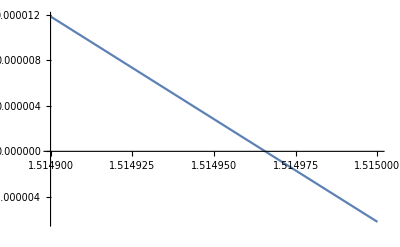

```mathematica
Plot[g[1,u],{u,1.5149,1.5150}]
```